```mathematica
a=Table[2^i+-3^j,{i,3},{j,3}]
b = Table[4*Power[-1,(i*(i+1))/2-((4*(4-1))/2)*Power[2,j]],{i,3},{j,3}]
```

{{-1,-7,-25},{1,-5,-23},{5,-1,-19}}

```mathematica
{{-4,-4,-4},{-4,-4,-4},{4,4,4}}
12*a
a+b
a*b
Det[a]
a^-1
```

{{-4,-4,-4},{-4,-4,-4},{4,4,4}}

{{-12,-84,-300},{12,-60,-276},{60,-12,-228}}

{{-5,-11,-29},{-3,-9,-27},{9,3,-15}}

{{4,28,100},{-4,20,92},{20,-4,-76}}

0

{{-1,-1/7,-1/25},{1,-1/5,-1/23},{1/5,-1,-1/19}}

```mathematica
12*a
a+b
a*b
Det[a]
a^-1
```

{{-12,-84,-300},{12,-60,-276},{60,-12,-228}}

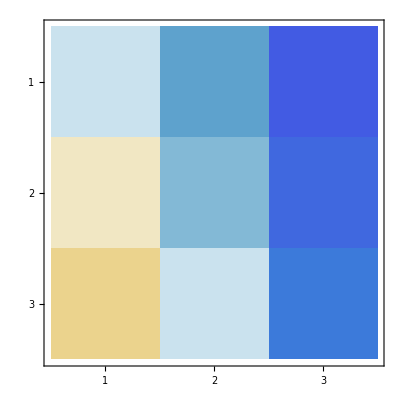

```mathematica
MatrixPlot[{{-12,-84,-300},{12,-60,-276},{60,-12,-228}}]
```

```mathematica
4*a
a+b
a*b
Det[a]
a^-1
```

{{-4,-28,-100},{4,-20,-92},{20,-4,-76}}

{{-5,-11,-29},{-3,-9,-27},{9,3,-15}}

{{4,28,100},{-4,20,92},{20,-4,-76}}

0

{{-1,-1/7,-1/25},{1,-1/5,-1/23},{1/5,-1,-1/19}}

```mathematica
ec1=4x+(2*4-1)*y+(4-5)*z == 4-4
ec2 = x+3*4*y-(7-4)*z == -2*4-5
ec3 =  2*4*x-(4+2)*y+(4-3)*z ==6*4-1
Solve[{ec1, ec2, ec3}, {x,y,z}]
```

4 x+7 y-z==0

x+12 y-3 z==-13

8 x-6 y+z==23

```mathematica
A={{4,7,-1},{1,12,-3},{8,-6,1},{0,-13,23}
B={0,-13,23}

X=LinearSolve[A,B]
```

{{4,7,-1},{1,12,-3},{8,-6,1}}

{0,-13,23}

{2,-1,1}

```mathematica
Total[X]
```

2

```mathematica
RowReduce[{{4,7,-1},{1,12,-3},{8,-6,1},{0,-13,23}]
```

```mathematica
RowReduce[A]
```

{{1,0,0},{0,1,0},{0,0,1}}

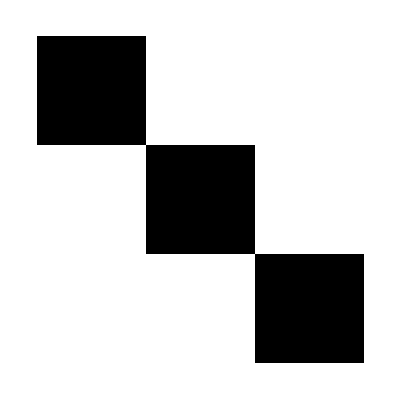

```mathematica
ArrayPlot[{{1,0,0},{0,1,0},{0,0,1}}]
```

```mathematica
A={{4,7,-1},{1,12,-2},{8,-6,1},{0,-13,23}}
```

```mathematica
{{4,7,-1},{1,12,-3},{8,-6,1},{0,-13,23}}
```

{{4,7,-1},{1,12,-3},{8,-6,1},{0,-13,23}}

```mathematica
RowReduce[A]
```

{{1,0,0},{0,1,0},{0,0,1},{0,0,0}}

```mathematica
RowReduce[{{12,7,-1},{1,12,-2},{3,-6,1}}]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MatrixForm[{{1,0,0},{0,1,0},{0,0,1}}]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Det[{{1,0,0},{0,1,0},{0,0,1}}]
```

1

```mathematica
RowReduce[({{4, 7, -1}, {1, 12, -2}, {8, -6, 1}})]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
RowReduce[A]
```

```mathematica
RowReduce[A]
```

RowReduce[A]

```mathematica
A=[{4,7,-1},{1,12,-2},{8,-6,1}]
```

```mathematica
RowReduce[A]
```

```mathematica
RowReduce[A]
```

RowReduce[A]

```mathematica
A={{4,7,-1},{1,12,-2},{8,-6,1}}
```

```mathematica
RowReduce[{{4,7,-1},{1,12,-2},{8,-6,1}}]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
RowReduce[{{1,2,3},{4,5,6},{7,8,9}}]
```

{{1,0,-1},{0,1,2},{0,0,0}}

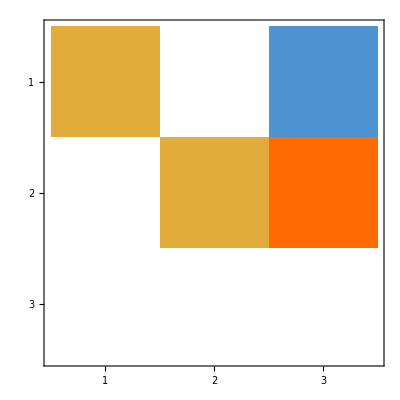

```mathematica
MatrixPlot[{{1,0,-1},{0,1,2},{0,0,0}}]
```

```mathematica
RowReduce[{{1,2,3},{4,5,6},{7,8,9}}]
```

{{1,0,-1},{0,1,2},{0,0,0}}

```mathematica
f1 = 4x1+(2*4-1)y1+(4-5)z1==4-4
f2 = x1+3*4y1-(7-4)z1==-2*4-5
f3 = (4+1)x1+(5*4-1)y1+(2*4-12)z1==-4-9
A={{4,7,-1},{1,12,-3},{5,19,-4}}
B= {{4,7,-1,0},{1,12,-3,-13},{5,19,-4,-13}}
MatrixRank[A]
MatrixRank[B]
B={0,-13,-13}
{a}.NullSpace[A]+LinearSolve[A,B]
```

4 x1+7 y1-z1==0

x1+12 y1-3 z1==-13

5 x1+19 y1-4 z1==-13

{{4,7,-1},{1,12,-3},{5,19,-4}}

{{4,7,-1,0},{1,12,-3,-13},{5,19,-4,-13}}

2

2

{0,-13,-13}

{91/41-9 a,-52/41+11 a,41 a}

```mathematica
MatrixForm[A]
```

(4 | 7 | -1
1 | 12 | -3
5 | 19 | -4)

```mathematica
M={{-1,-7,-25},{1,-5,-23},{5,-1,-19}}
 Eigenvalues[M]
```

{{-1,-7,-25},{1,-5,-23},{5,-1,-19}}

{1/2 (-25+ⅈ √287),1/2 (-25-ⅈ √287),0}

```mathematica
Eigenvectors[M]
```

{{-(-287 ⅈ+√287)/(77 ⅈ+5 √287),-(-217 ⅈ-√287)/(77 ⅈ+5 √287),1},{-(287 ⅈ+√287)/(-77 ⅈ+5 √287),-(217 ⅈ-√287)/(-77 ⅈ+5 √287),1},{3,-4,1}}